```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/368nm.dat"]
data1hour=Drop[data1, None,1]
data2 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/412nm.dat"]
data2hour=Drop[data2,None,1]
data3 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/500nm.dat"]
data3hour=Drop[data3,None,1]
data4 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/610nm.dat"]
data4hour=Drop[data4,None,1]
data5 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/675nm.dat"]
data5hour=Drop[data5,None,1]
data6= Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/778nm.dat"]
data6hour=Drop[data6,None,1]
data7 = Import["/net/home/f09/bajennissen/research/DAY182/tau_day_data/862nm.dat"]
data7hour=Drop[data7,None,1]
```

{{182.312,7.483,0.174},{182.317,7.617,0.172},{182.322,7.733,0.159},{182.332,7.967,0.16},{182.346,8.3,0.189},{182.51,12.25,0.088},{182.541,12.983,0.18},{182.549,13.167,0.134}}

{{7.483,0.174},{7.617,0.172},{7.733,0.159},{7.967,0.16},{8.3,0.189},{12.25,0.088},{12.983,0.18},{13.167,0.134}}

{{182.312,7.48333,0.166801},{182.317,7.61667,0.16725},{182.322,7.73333,0.155045},{182.332,7.96667,0.156818},{182.346,8.3,0.177807},{182.51,12.25,0.127583},{182.541,12.9833,0.202755},{182.549,13.1667,0.162361}}

{{7.48333,0.166801},{7.61667,0.16725},{7.73333,0.155045},{7.96667,0.156818},{8.3,0.177807},{12.25,0.127583},{12.9833,0.202755},{13.1667,0.162361}}

{{182.312,7.48333,0.126892},{182.317,7.61667,0.126305},{182.322,7.73333,0.11394},{182.332,7.96667,0.109706},{182.346,8.3,0.120339},{182.51,12.25,0.166822},{182.541,12.9833,0.129172},{182.549,13.1667,0.10915}}

{{7.48333,0.126892},{7.61667,0.126305},{7.73333,0.11394},{7.96667,0.109706},{8.3,0.120339},{12.25,0.166822},{12.9833,0.129172},{13.1667,0.10915}}

{{182.312,7.48333,0.149979},{182.317,7.61667,0.147658},{182.322,7.73333,0.133719},{182.332,7.96667,0.129066},{182.346,8.3,0.137881},{182.51,12.25,0.120136},{182.541,12.9833,0.155126},{182.549,13.1667,0.13639}}

{{7.48333,0.149979},{7.61667,0.147658},{7.73333,0.133719},{7.96667,0.129066},{8.3,0.137881},{12.25,0.120136},{12.9833,0.155126},{13.1667,0.13639}}

{{182.312,7.48333,0.127971},{182.317,7.61667,0.127124},{182.322,7.73333,0.111714},{182.332,7.96667,0.112169},{182.346,8.3,0.125465},{182.51,12.25,0.110683},{182.541,12.9833,0.159352},{182.549,13.1667,0.140666}}

{{7.48333,0.127971},{7.61667,0.127124},{7.73333,0.111714},{7.96667,0.112169},{8.3,0.125465},{12.25,0.110683},{12.9833,0.159352},{13.1667,0.140666}}

{{182.312,7.48333,0.142344},{182.317,7.61667,0.141095},{182.322,7.73333,0.128951},{182.332,7.96667,0.13005},{182.346,8.3,0.160987},{182.51,12.25,0.144896},{182.541,12.9833,0.220668},{182.549,13.1667,0.169591}}

{{7.48333,0.142344},{7.61667,0.141095},{7.73333,0.128951},{7.96667,0.13005},{8.3,0.160987},{12.25,0.144896},{12.9833,0.220668},{13.1667,0.169591}}

{{182.312,7.48333,0.129257},{182.317,7.61667,0.12853},{182.322,7.73333,0.113986},{182.332,7.96667,0.121918},{182.346,8.3,0.168426},{182.51,12.25,0.124127},{182.541,12.9833,0.254275},{182.549,13.1667,0.17229}}

{{7.48333,0.129257},{7.61667,0.12853},{7.73333,0.113986},{7.96667,0.121918},{8.3,0.168426},{12.25,0.124127},{12.9833,0.254275},{13.1667,0.17229}}

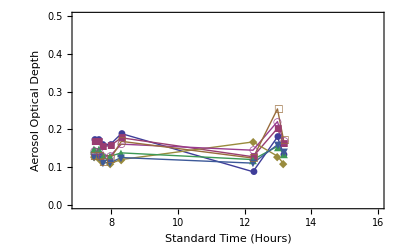

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{1.1,-0.4}, LegendSize->{0.5,0.75},PlotRange->{{7,16},{0,.5}},Frame->True, AxesOrigin-> {7,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 182 July 1st, 2010"}}]
```